```mathematica
data=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/EECS545-Project/results/15n-0n-on-15n_0420-0820.csv","Numeric"->True];
data=Delete[data, 1];
{baseline, gnn}=GatherBy[data,First];
baseline=Drop[#,{2,3}]&/@(Drop[#,{1,6}]&/@baseline);
gnn=Drop[#,{2,3}]&/@(Drop[#,{1,6}]&/@gnn);
```

```mathematica
(*{stime|walltime|proctime}*)
baselineWall=Part[#,2]&/@baseline;
gnnWall=Part[#,2]&/@gnn;
transferLsize=Min[Length[baselineWall],Length[gnnWall]]
baselineWallnormal=baselineWall[[1;;100]];
baselineWalltransferS=baselineWall[[101;;200]];
baselineWalltransferM=baselineWall[[201;;300]];
baselineWalltransferL=baselineWall[[301;;transferLsize]];
gnnWallnormal=gnnWall[[1;;100]];
gnnWalltransferS=gnnWall[[101;;200]];
gnnWalltransferM=gnnWall[[201;;300]];
gnnWalltransferL=gnnWall[[301;;transferLsize]];
```

400

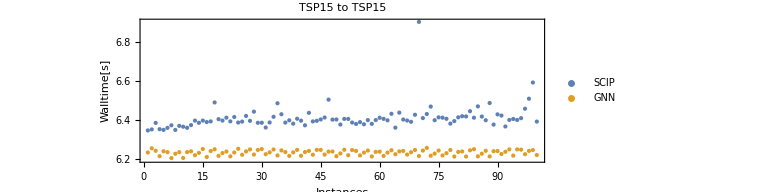

```mathematica
p1=Show[
ListPlot[{baselineWallnormal,gnnWallnormal},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.8}]
],
PlotRange->{Automatic,{6.2, 6.9}},
PlotLabel->Style["TSP15 to TSP15"],
AxesOrigin->{0,0},
AspectRatio->1/3,
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/EECS545-Project/results/Plots/15-15.png",p1];
```

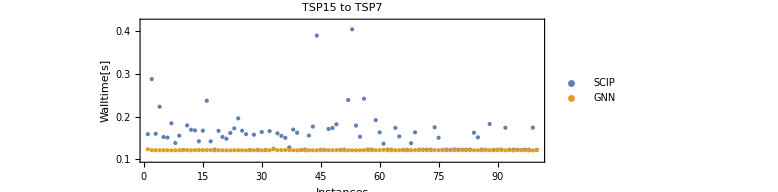

```mathematica
p1=Show[
ListPlot[{baselineWalltransferS,gnnWalltransferS},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.8}]
],
PlotRange->{Automatic,{0.1,0.42}},
PlotLabel->Style["TSP15 to TSP7"],
AxesOrigin->{0,0},
AspectRatio->1/3,
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/EECS545-Project/results/Plots/15-7(from15-15).png",p1];
```

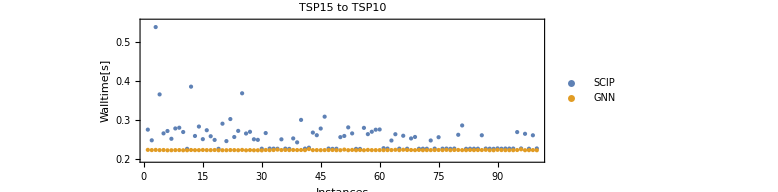

```mathematica
p1=Show[
ListPlot[{baselineWalltransferM,gnnWalltransferM},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.8}]
],
PlotRange->{Automatic,{0.2,0.55}},
PlotLabel->Style["TSP15 to TSP10"],
AxesOrigin->{0,0},
AspectRatio->1/3,
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/EECS545-Project/results/Plots/15-10(from15-15).png",p1];
```

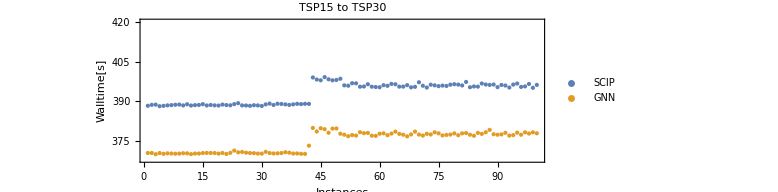

```mathematica
p1=Show[
ListPlot[{baselineWalltransferL,gnnWalltransferL},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.8}]
],
PlotRange->{Automatic,{368,420}},
PlotLabel->Style["TSP15 to TSP30"],
AxesOrigin->{0,0},
AspectRatio->1/3,
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/EECS545-Project/results/Plots/15-30(from15-15).png",p1];
```

```mathematica
Mean[baselineWalltransferL-gnnWalltransferL]/Mean[baselineWalltransferL]*100
```

4.66999